```mathematica
img=-Graphics-
```

-Graphics-

```mathematica
(*PixelateImage[img_Image,pixelSize_Integer:20]:=
Module[{small,scaled},
small=ImageResize[img,Scaled[1/pixelSize]];
scaled=ImageResize[small,ImageDimensions[img]];
scaled
]
*)
```

```mathematica
(*PixelateImage[img]*)
```

```mathematica
(*x=EdgeDetect[img]*)
```

```mathematica
(*ContourDetect[x]*)
```

```mathematica
x=CurrentImage[]
```

-Graphics-

```mathematica
ImageRestyle[x,-Graphics-, PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
baseAudio=AudioCapture[]
```

```mathematica
baseAudio=AudioTrim[baseAudio]
```

```mathematica
stft=ShortTimeFourier[baseAudio]
```

ShortTimeFourierData[<<Data dimensions: {323, 512}, SampleRate: 44100>>]

```mathematica
f0=AudioLocalMeasurements[baseAudio, "FundamentalFrequency"]
```

TimeSeries[…]

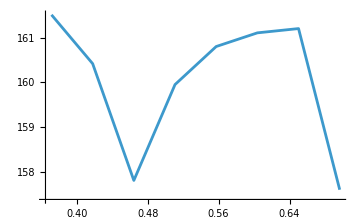

```mathematica
ListLinePlot[f0,ImageSize->Medium]
```

```mathematica
Audio[InverseShortTimeFourier[stft]]
```

```mathematica
s=AudioData[frames[[1]]];
```

```mathematica
autoCorr=ListCorrelate[s,s,{1,-1},0]
```

{{132.291}}

```mathematica
frameSize=0.05; (*50 ms frames*)
frames=AudioPartition[baseAudio,frameSize,frameSize];
```

```mathematica
estimatePitchFrame[af_]:=Module[{samples,sampleRate,autoCorr,minLag,maxLag,lags,acSubset,peakIndex,peakLag,freq},samples=AudioData[af,"Real32"];
sampleRate=AudioSampleRate[af];
autoCorr=ListCorrelate[samples,samples,{1,-1},0];
(*Reasonable human pitch range~50 Hz to 1000 Hz*)minLag=Floor[sampleRate/1000];(* ~1000 Hz*)maxLag=Ceiling[sampleRate/50];(* ~50 Hz*)lags=Range[minLag,maxLag];
acSubset=autoCorr[[lags]];(*This is now a proper list subset*)peakIndex=First@Ordering[acSubset,-1];
peakLag=lags[[peakIndex]];
freq=sampleRate/peakLag;
freq];
```

```mathematica
estimatePitchFrame[frames[[1]]]
```

Part::pkspec1: The expression … cannot be used as a part specification.

980